## Fixed M_Z'=10 TeV, Fixed Brane parameter = 0.5, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 ( (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime10=10;
MassNu=0.1;
CvL05=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.5)
```

0.499871

```mathematica
Zprime10decayfixedmass05[CvR_]:=MassZprime10/(12π)(1/4(CvL05+CvR)^2+1/4(CvL05-CvR)^2+2(MassNu/MassZprime10)^2(1/4(CvL05+CvR)^2-1/2(CvL05+CvR)^2))√(1-4(MassNu/MassZprime10)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime10decayfixedmass05Table=Table[{Q[i],Zprime10decayfixedmass05[Q[i]]},{i,0,Npt}]
```

{{0.,33.1302},{0.1,34.4548},{0.2,38.4312},{0.3,45.0593},{0.4,54.3392},{0.5,66.2709},{0.6,80.8544},{0.7,98.0897},{0.8,117.977},{0.9,140.516},{1.,165.706}}

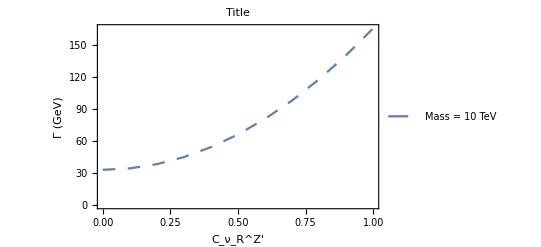

```mathematica
PlotZprimeDecayFixed1005=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Medium]},PlotLegends->{"Mass = 10 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

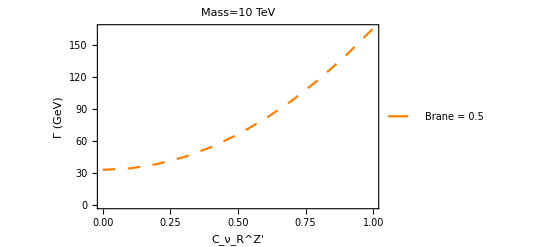

```mathematica
PlotZprimeDecayFixed1005B=ListPlot[%%, Joined-> True,PlotStyle->{Orange,Dashing[Medium]},PlotLegends->{"Brane = 0.5"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 10 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime10decayfixedmass05Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 33.1302
0.1 | 34.4548
0.2 | 38.4312
0.3 | 45.0593
0.4 | 54.3392
0.5 | 66.2709
0.6 | 80.8544
0.7 | 98.0897
0.8 | 117.977
0.9 | 140.516
1. | 165.706

## Fixed M_Z'=8 TeV, Fixed Brane parameter = 0.5, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime8=8;
MassNu=0.1;
CvL05=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.5)
```

0.499871

```mathematica
Zprime8decayfixedmass05[CvR_]:=MassZprime8/(12π)(1/4(CvL05+CvR)^2+1/4(CvL05-CvR)^2+2(MassNu/MassZprime8)^2(1/4(CvL05+CvR)^2-1/2(CvL05+CvR)^2))√(1-4(MassNu/MassZprime8)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime8decayfixedmass05Table=Table[{Q[i],Zprime8decayfixedmass05[Q[i]]},{i,0,Npt}]
```

{{0.,26.4997},{0.1,27.5586},{0.2,30.7385},{0.3,36.0396},{0.4,43.4617},{0.5,53.0048},{0.6,64.6691},{0.7,78.4544},{0.8,94.3607},{0.9,112.388},{1.,132.537}}

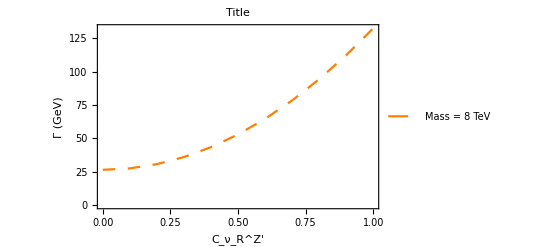

```mathematica
PlotZprimeDecayFixed805=ListPlot[%, Joined-> True,PlotStyle->{Orange, Dashing[Medium]},PlotLegends->{"Mass = 8 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

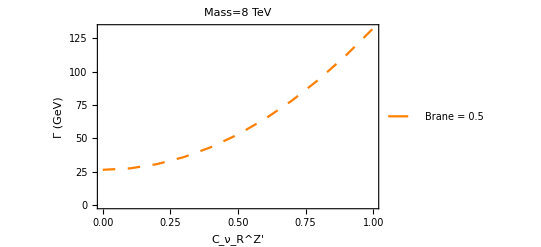

```mathematica
PlotZprimeDecayFixed805B=ListPlot[%%, Joined-> True,PlotStyle->{Orange,Dashing[Medium]},PlotLegends->{"Brane = 0.5"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 8 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime8decayfixedmass05Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 26.4997
0.1 | 27.5586
0.2 | 30.7385
0.3 | 36.0396
0.4 | 43.4617
0.5 | 53.0048
0.6 | 64.6691
0.7 | 78.4544
0.8 | 94.3607
0.9 | 112.388
1. | 132.537

## Fixed M_Z'=5 TeV, Fixed Brane parameter = 0.4, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime5=5;
MassNu=0.1;
CvL05=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.5)
```

0.499871

```mathematica
Zprime5decayfixedmass05[CvR_]:=MassZprime5/(12π)(1/4(CvL05+CvR)^2+1/4(CvL05-CvR)^2+2(MassNu/MassZprime5)^2(1/4(CvL05+CvR)^2-1/2(CvL05+CvR)^2))√(1-4(MassNu/MassZprime5)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime5decayfixedmass05Table=Table[{Q[i],Zprime5decayfixedmass05[Q[i]]},{i,0,Npt}]
```

{{0.,16.5502},{0.1,17.2099},{0.2,19.1943},{0.3,22.5034},{0.4,27.1372},{0.5,33.0957},{0.6,40.3789},{0.7,48.9868},{0.8,58.9194},{0.9,70.1767},{1.,82.7587}}

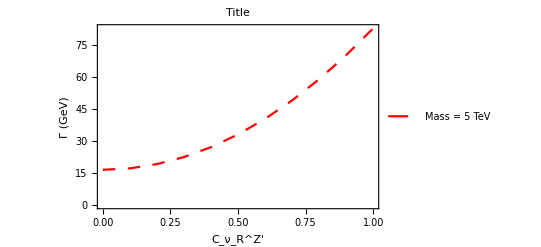

```mathematica
PlotZprimeDecayFixed505=ListPlot[%, Joined-> True,PlotStyle->{Red, Dashing[Medium]},PlotLegends->{"Mass = 5 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

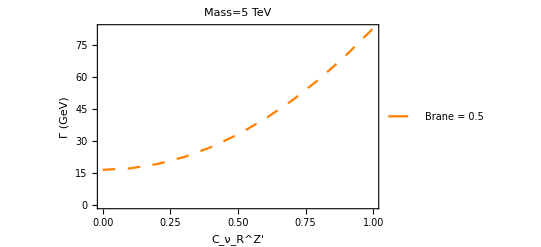

```mathematica
PlotZprimeDecayFixed505B=ListPlot[%%, Joined-> True,PlotStyle->{Orange,Dashing[Medium]},PlotLegends->{"Brane = 0.5"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 5 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime5decayfixedmass05Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 16.5502
0.1 | 17.2099
0.2 | 19.1943
0.3 | 22.5034
0.4 | 27.1372
0.5 | 33.0957
0.6 | 40.3789
0.7 | 48.9868
0.8 | 58.9194
0.9 | 70.1767
1. | 82.7587

## OverLay

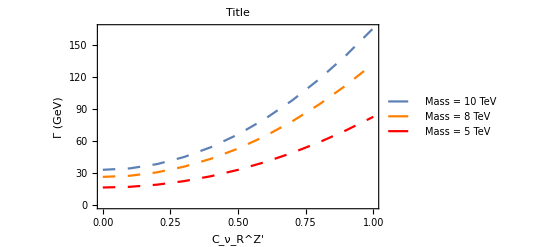

```mathematica
Show[PlotZprimeDecayFixed1005,PlotZprimeDecayFixed805,PlotZprimeDecayFixed505]
```

## OverLay 2

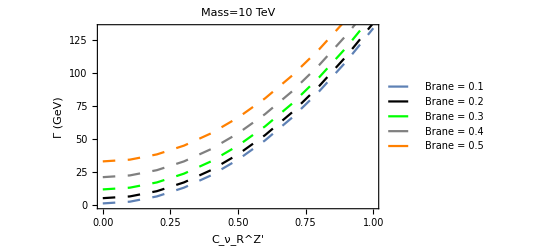

```mathematica
Show[PlotZprimeDecayFixed1001B,PlotZprimeDecayFixed1002B,PlotZprimeDecayFixed1003B,PlotZprimeDecayFixed1004B,PlotZprimeDecayFixed1005B]
```

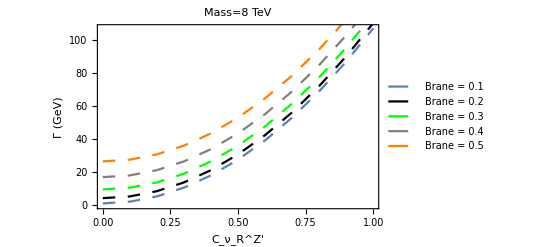

```mathematica
Show[PlotZprimeDecayFixed801B,PlotZprimeDecayFixed802B,PlotZprimeDecayFixed803B,PlotZprimeDecayFixed804B,PlotZprimeDecayFixed805B]
```

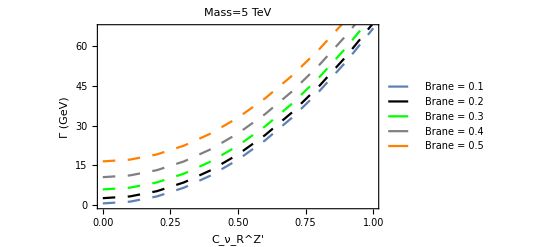

```mathematica
Show[PlotZprimeDecayFixed501B,PlotZprimeDecayFixed502B,PlotZprimeDecayFixed503B,PlotZprimeDecayFixed504B,PlotZprimeDecayFixed505B]
```